Function[{f$},Norm[f$[tmax]-{0.412698,0}]≤tol]

Function[{f$},Norm[f$[tmax]-{1,1}]≤tol]

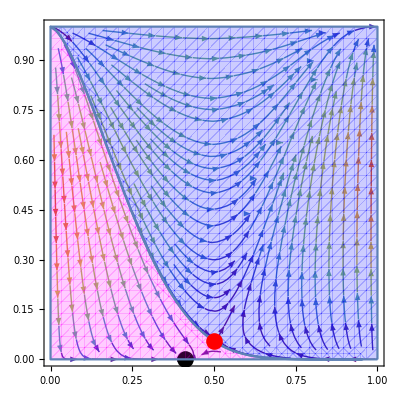

0.244123

0.856626

0

1.

```mathematica
tmax=400;
tol=0.05;

p=0.7;
e=0.9;
d=0.5;
c = 0.5;
gamma = 1;

(*Solution to ODE that maps t to {x[t],y[t]}*)
sol[x0_?NumericQ,y0_?NumericQ]:=First@NDSolve[{x[0]==x0,y[0]==y0,x'[t]==x[t](1-x[t])(e* p(1-d x[t])-c(1-y[t])),y'[t]==gamma y[t](1-y[t])(2x[t]-1)},{x,y},{t,0,tmax}]/.HoldPattern[{x->xi_,y->yi_}]:>Function[{t},{xi[t],yi[t]}];
(*Create function that takes a solution as argument and checks if it's close to attractor at tmax*)
MakeBasinTest[{x0_,y0_}]:=Function[{f},Norm[f[tmax]-{x0,y0}]≤tol];

inCenterBasinQ=MakeBasinTest[{(e p -c)/(e d p),0}]
inCenterBasinQ2=MakeBasinTest[{1,1}]

xs0=0.5;
ys0 = (c-e p (1-d/2))/c;
xs1=(e p -c)/(e d p);
ys1= 0;


Show[StreamPlot[{x(1-x)(e* p(1-d x)-c(1-y)),y(1-y)(2x-1)},{x,0,1},{y,0,1},StreamColorFunction->"Rainbow"],
RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1},PlotPoints->30,MaxRecursion->1,PlotStyle->{Magenta,Opacity[0.2]}],RegionPlot[inCenterBasinQ2[sol[x0,y0]],{x0,0,1},{y0,0,1},PlotPoints->30,MaxRecursion->1,PlotStyle->{Blue,Opacity[0.2]}],Graphics[{PointSize[0.03],Red,Point[{xs0,ys0}]}],
Graphics[{PointSize[0.03],Black,Point[{xs1,ys1}]}]]

area=Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]]
CooperationFraction=area (e p -c)/(e d p) + (1-area)
```

```mathematica
RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1},PlotPoints->30,MaxRecursion->1,PlotStyle->{Orange,Opacity[0.2]}],
```

0.643142

```mathematica
(* Generates a table with area of basin towards (1,1) *)

Export["table_area_3.tsv",Table[c = i;p = j;Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]],{i,0.01,1,0.25},{j,0.01,1,0.25}]]
```

table_area_3.tsv

```mathematica
(* Generates a table with fraction of cooperation (the basin changes: goes towards (0,0) if there is no fixed point on the x axis, or towards it if there is *)

Export["coop9.tsv",Table[c = i;p = j; If[0< (e p -c)/(e d p)<1,inCenterBasinQ=MakeBasinTest[{(e p -c)/(e d p),0}];a=Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]];a (e p -c)/(e d p) + (1-a),inCenterBasinQ=MakeBasinTest[{0,0}];a=Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]]; 1-a] ,{i,0.01,1.01,0.125},{j,0.01,1.01,0.125}]]
```

coop9.tsv

```mathematica
(* Computes the fraction of cooperation for p and c given *)

p=0.5;
c = 0.4;

If[0< (e p -c)/(e d p)<=1,inCenterBasinQ=MakeBasinTest[{(e p -c)/(e d p),0}];a=Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]];a (e p -c)/(e d p) + (1-a),inCenterBasinQ=MakeBasinTest[{0,0}];a=Area[DiscretizeGraphics[RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,0,1},{y0,0,1}]]]; 1-a]
```

0.741969